```mathematica
Needs["ComputerArithmetic`"]
here=NotebookDirectory[]
```

/home/WIN/tomha/Dropbox/Delaware/Codes/DEA_Wrap/

```mathematica
SetDirectory[here];
FileNames["*.csv"]
```

{data.csv,Gx.csv,InGaN_Fixed.csv,InGaN__Sch_OpticalStudy2.csv,InGaN_Sch_OpticalStudy.csv}

```mathematica
data=Import[here<>"InGaN_Sch_OpticalStudy2.csv","table"]/."NaN"->-1;
```

```mathematica
Dimensions[data]
```

{14,6794}

```mathematica
Count[data[[-5]],-1]
```

6794

```mathematica
722./1115
```

0.647534

```mathematica
FoM=-8; (* -8 for JscOpt, -5 for eta *)
```

```mathematica
data[[All,1]]
```

{500.,50.,60.,100.,0.5,9.19525,9.19525,8.67183,9.71867,-1,-1,-1,-1,-1}

```mathematica
colors=data[[-6,All]]/data[[-7,All]]; (* This is JscOptp/JscOpts *)
colors=colors+0*data[[-8]];
cmin=Mean[DeleteCases[colors,-1,-1]]-1.StandardDeviation[DeleteCases[colors,-1,-1]]
cmin=cmin+0*Min[DeleteCases[colors,-1,-1]];
cmax=Mean[DeleteCases[colors,-1,-1]]+1.StandardDeviation[DeleteCases[colors,-1,-1]]
cmax=cmax+0*Max[DeleteCases[colors,-1,-1]];
(*cmin=25;
cmax=35;*)
cmin = 0.7
cmax=1.3
cscale=cmax-cmin
maxAt=Ordering[data[[FoM,All]],-1][[1]]
data[[FoM,maxAt]]
```

0.62711

1.1404

0.7

1.3

0.6

6706

19.3909

```mathematica
paramNo=5;
xvals=data[[paramNo,All]];
(*If[paramNo==1,xvals=xvals*(1-data[[2,All]])+0*data[[1,All]]];
If[paramNo==3,xvals=xvals*(data[[7,All]]-0.7)];*)
yvals=data[[FoM,All]];
xmin=Min[xvals]
xmin=xmin-0.2*0;
xmax=Max[xvals]
xmax=0.9xmax+0*0.2;
xscale=xmax-xmin
ticks=True;
If[paramNo==6,ticks=Table[{i,2^i},{i,xmin,xmax,2}]];
ymin = 5;
ymax=20;
yscale=ymax-ymin
```

0.01

0.99

0.881

15

```mathematica
resultsPlot=Show[ListPointPlot3D[Transpose[{xvals,yvals,colors}],AxesLabel->{Framed[Style["ζ",16,Bold, SingleLetterItalics->True],FrameStyle->None,FrameMargins->0],Framed[Rotate[Style["J_SC^Opt (mA/cm^2)",16,Bold,SingleLetterItalics->False],Pi/2],FrameStyle->None,FrameMargins->20]},ColorFunctionScaling->False,ViewPoint->{0,0,Infinity},ColorFunction->Function[{x,y,z},ColorData["Rainbow"][(z-cmin)/cscale]],PlotRange->{{xmin,xmax},{ymin,ymax},Full},PlotLegends->BarLegend[{"Rainbow",{cmin,cmax}},ColorFunctionScaling->True],Ticks->{ticks,True,False}],Graphics3D[{Lighting->None,Glow[ColorData["Rainbow"][(colors[[maxAt]]-cmin)/cscale]],Scale[Sphere[{xvals[[maxAt]],yvals[[maxAt]],colors[[maxAt]]}, 0.015],{xscale,yscale,cscale}]},{CapForm[None],Lighting->Automatic,Tube[{{xvals[[maxAt]],yvals[[maxAt]],0},{xvals[[maxAt]],yvals[[maxAt]],colors[[maxAt]]}},15]}]]
```

-Graphics3D-

```mathematica
Export[here<>"zeta_J_InGaN.eps",resultsPlot,"eps"]
```

/home/WIN/tomha/Dropbox/Delaware/Codes/DEA_Wrap/zeta_J_InGaN.eps

```mathematica
BestCell=data[[1;;8,maxAt]];
Print["L_o/L_x: ",BestCell[[1]](1-BestCell[[2]])," L_s/L_x:",BestCell[[2]], " A:", BestCell[[3]](BestCell[[7]]-0.7), " κ:", BestCell[[4]]," ϕ:", BestCell[[5]]," α:", 2^BestCell[[6]]," E_g^*:",BestCell[[7]]," L_z:",BestCell[[8]], " η:",data[[-5,maxAt]]," J_SC^Opt:",data[[-8,maxAt]] ]
```

L_o/L_x: 0.1643 L_s/L_x:0.47 A:1.3 κ:4.02 ϕ:0.35 α:256. E_g^*:2. L_z:494. η:38.2899 J_SC^Opt:42.564

```mathematica
data[[-9,maxAt]]
```

38.2899

```mathematica
JOpt_s: 39.899863
```

JOpt_s:39.8999

```mathematica
data[[;;,maxAt]]
```

{0.31,0.47,1.,4.02,0.35,8.,2.,494.,38.2899,42.564,42.436,42.692,38.2899,1.08,42.0226,1.183,0.770223}

```mathematica
Point[{data[[2,maxAt]],data[[6,maxAt]],1.2data[[8,maxAt]]/data[[7,maxAt]]}]
```

Point[{0.78,7.04,193.75}]

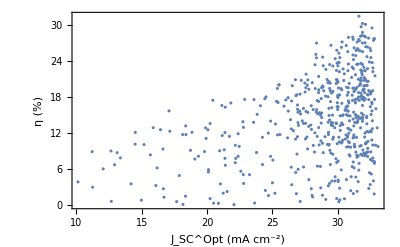

```mathematica
resultsPlot=ListPlot[Transpose[{data[[-8,All]],data[[FoM,All]]/.-1->Infinity}],PlotRange->Automatic,FrameLabel->{Style["J_SC^Opt (mA cm^-2)",SingleLetterItalics->False],"η (%)"},Frame->{True,True,False,False}]
```

```mathematica
Max[data[[-8,All]]]
```

33.0924

```mathematica
data[[;;,500]]
```

{0.16,0.72,0.98,1.9,0.,8.,1.5,225.,33.0821,33.0821,33.1664,32.9979,-1,-1,-1,-1,-1}

```mathematica
Max[data[[-8,maxAt]]]
```

31.6318

```mathematica
range=All;
filter=1+( yvals-Abs[yvals])/2;
A=data[[3,range]]*(data[[7,range]]-0.7)*filter;
kappa=data[[4,range]];
phi=data[[5,range]];
alpha=2^data[[6,range]];
Eg0=data[[7,range]]*filter;
nmLi=data[[8,range]];
Eg[z_]:=Eg0-A+A*((0.5*(Sin[2*Pi*z*kappa/nmLi-2*Pi*phi]+1))^alpha)
```

```mathematica
xpoint=Table[x,{x,0,Max[nmLi]}];
```

```mathematica
avEg=Reap[For[i=1,i<=Length[nmLi],i++,
Sow[Quiet[NIntegrate[Eg[z][[i]],{z,0,nmLi[[i]]}]/nmLi[[i]]]]
]
][[2,1]];
```

9.62642/(1-Sin[0.125664-0.0978727 z])^3.267

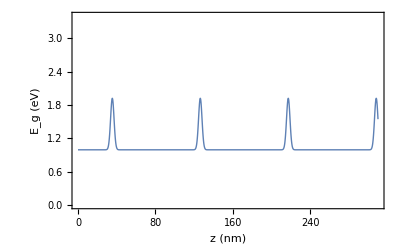

```mathematica
resultsPlot=Plot[Eg[z][[maxAt]],{z,0,nmLi[[maxAt]]},FrameLabel->{Framed[Style["z (nm)",14,Bold],FrameStyle->None,FrameMargins->0],Framed[Rotate[Style["E_g (eV)",14,Bold],0],FrameStyle->None,FrameMargins->10]},Frame->{True,True,False,False},PlotRange->{0,3.4},PlotStyle->Thick]
```

```mathematica
here="C:\\Users\\Tom\\Dropbox\\Delaware\\Solar Cell Presentations\\Optics and Photonics\\"
Export[here<>"optEg_InGaN.eps",resultsPlot,"eps"];
```

C:\Users\Tom\Dropbox\Delaware\Solar Cell Presentations\Optics and Photonics\

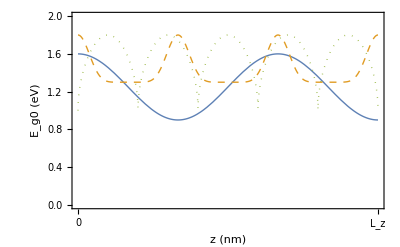

```mathematica
A=.;
kappa=.;
phi=.;
alpha=.;
Eg0=.;
nmLi=200;

ExampleEg=Plot[{Eg[z]/.{A->0.7,kappa->1.5,phi->0.75,alpha->2^0,Eg0->1.6},Eg[z]/.{A->0.5,kappa->3,phi->0.75,alpha->2^2,Eg0->1.8},Eg[z]/.{A->0.8,kappa->5,phi->0.25,alpha->2^-2,Eg0->1.8}},{z,0,200},PlotRange->{0,2},FrameLabel->{Framed[Style["z (nm)",14,Bold],FrameStyle->None,FrameMargins->0],Framed[Rotate[Style["E_g0 (eV)",14,Bold],0],FrameStyle->None,FrameMargins->10]},Frame->{{True,False},{True,False}},PlotStyle->{Thick,Directive[Thick,Dashed],Directive[Thick,Dotted]},FrameTicks->{{Automatic,None},{{{0,0},{200,"L_z"}},None}}]
```

```mathematica
here="C:\\Users\\Tom\\Dropbox\\Delaware\\Solar Cell Presentations\\Optics and Photonics\\"
Export[here<>"ExampleEg.eps",ExampleEg,"eps"];
```

C:\Users\Tom\Dropbox\Delaware\Solar Cell Presentations\Optics and Photonics\

```mathematica
here="C:\\Users\\Tom\\Dropbox\\Delaware\\Solar Cell Presentations\\Optics and Photonics\\"
data=Import[here<>"testDetails.csv","csv"];
```

C:\Users\Tom\Dropbox\Delaware\Solar Cell Presentations\Optics and Photonics\

```mathematica
data[[1]]
```

{350,6,0.000033452,0.012306}

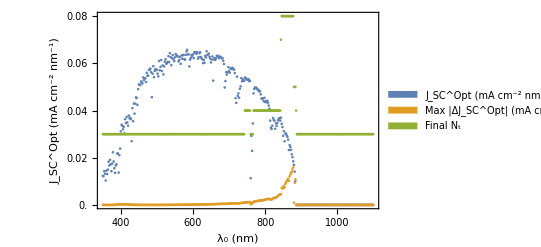

```mathematica
NtConverge=ListPlot[{Transpose[{data[[All,1]],200data[[All,4]]}],Transpose[{data[[All,1]],200data[[All,3]]}],Transpose[{data[[All,1]],data[[All,2]]}]},Frame->{{True,True},{True,False}},FrameTicks->{{Table[{i,i/200},{i,0.,16,2}],Table[{i,i},{i,0,16,4}]},{True,False}},PlotRangePadding->1,PlotLegends->SwatchLegend[{"J_SC^Opt (mA cm^-2 nm^-1)","Max |ΔJ_SC^Opt| (mA cm^-2 nm^-1)","Final N_t"}],FrameLabel->{"λ_0 (nm)","J_SC^Opt (mA cm^-2 nm^-1)",,"N_t"}]
```

```mathematica
Export[here<>"NtConverge.eps",NtConverge,"eps"]
```

C:\Users\Tom\Dropbox\Delaware\Solar Cell Presentations\Optics and Photonics\NtConverge.eps